## Eigenmodes of Separable Geometry of Laplacian

### Spherical Coord

```mathematica
ψ[l_,m_,n_,r_,θ_,ϕ_] := BesselJ[l+1/2, j[l,n] r]/Sqrt[r]  SphericalHarmonicY[l,m,θ,ϕ];
```

```mathematica
λ[l_,n_] := -j[l,n]^2/a^2;
```

### Rectangular Coord

```mathematica
ψ[x_,y_,z_,m_, n_,o_] = Sin[(n Pi x)/a]Sin[(m Pi y)/b]Sin[(o Pi z)/c]
```

```mathematica
λ[m_,n_,o_]=-((m Pi)/a)^2-((n Pi)/b)^2-((o Pi)/c)^2
```

### 2D Cylindrical Coord

```mathematica
j[m_, n_] := BesselJZero[m,n]//N;
```

```mathematica
ψ[m_,n_,r_,θ_]:=BesselJ[m,(j[m,n] r)/a] Exp[ⅈ m θ];
```

```mathematica
λ1[m_,n_] = - (j[m, n]/a)^2;
```

#### Example

```mathematica
ψ[m_,n_,r_,θ_] = Sin[k[m] θ] BesselJ[k[m],j[m,n] r/a];
```

```mathematica
λ[m_,n_] = -j[m,n]^2/a^2;
```

```mathematica
k[m_] = m Pi/α;
```

```mathematica
c[m_,n_]=Integrate[ψ[m,n]r,{r,0,a},{θ,0,α}]/Integrate[ψ[m,n] ψ[m,n] r,{r,0,a},{θ,0,α}]
```

```mathematica
c[m_,n_] = Integrate[r (-1) ψ[m,n,r,θ],{r,0,a},{θ,0,α},Assumptions->a>0&&α>0&&j[m,n]>0&&a>0&&m>0]/(λ[m,n] Integrate[r  ψ[m,n,r,θ]^2,{r,0,a},{θ,0,α},Assumptions->a>0&&α>0&&j[m,n]>0&&a>0&&m>0])
```

```mathematica
ϕ[r_,θ_] = Sum[c[m,n] ψ[m,n,r,θ],{m,1,10},{n,1,10}];
```

### 3D Cylindrical Coord

## Fourier Transform

```mathematica
FourierTransform[f[x],x,-k] Sqrt[2Pi]
```

```mathematica
InverseFourierTransform[ T̃[k],k,-x]/Sqrt[2Pi]
```

## FTCS Method for heat Eqn

```mathematica
Subscript[T, j]^(n+1)=Subscript[T, j]^n+Δt Subscript[S, j]^n+(χ Δt)/Δx^2(Subscript[T, j+1]^n-2 Subscript[T, j]^n+Subscript[T, j-1]^n).
```

```mathematica
Clear["Global`*"];
```

### Declare the recursion function

```mathematica
T[j_,n_] := T[j,n] = T[j,n-1]+Δt S[j,n-1] + (χ Δt)/Δx^2(T[j+1,n-1] -2T[j,n-1]+T[j-1,n-1])
```

However determine the Tm and T0 is required additionally.

### Boundary Condition

```mathematica
T[0,n_] := T1[t]/.t->n Δt;
M=10;T[M,n_] := T2[t]/.t->n Δt
```

### Initial Condition

```mathematica
T[j_,0] := T0[x]/.x-> j Δx
```

### Specify the Grid size

```mathematica
L=1; χ = 1/4;Δt = 0.01;Δx = L/M;S[j_,n_] = 0;
```

```mathematica
T0[x_] = x^2(1-x);
T1[t_] = t/(1+3t);T2[t_] = 0;
```

### Plot

```mathematica
ListAnimate[Table[ListPlot[Table[{Δx j, T[j,n]},{j,0,M}],Joined->True,PlotRange->{0,.4},AxesLabel->{"x",""},PlotLabel->"T[x,t],t="<>ToString[Δt n]],{n,0,200,10}]]
```

## CTCS Method for heat Eqn

### Equation

```mathematica
Subscript[T, j]^(n+1)=1/2(Subscript[T, j+1]^(n-1)+Subscript[T, j-1]^(n-1))+2Δt Subscript[S, j]^n+(2χ Δt)/Δx^2(Subscript[T, j+1]^n-2 Subscript[T, j]^n+Subscript[T, j-1]^n)
```

### Von Neumann Stability Analysis

```mathematica
ξ^2+ 8δ sin^2(k Δx/2)ξ-cos k Δx=0
```

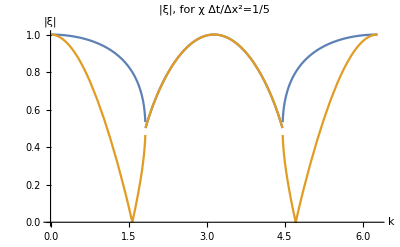

```mathematica
sol =Solve[ξ^2+8δ Sin[(k /2)]^2ξ-Cos[ k] ==0,ξ];
Plot[Evaluate[Abs[(ξ/.sol)]/.δ->1/5],{k,0,2Pi},AxesLabel->{"k","|ξ|"},PlotLabel->"|ξ|, for χ Δt/Δx^2=1/5"]
```

## The Crank-Nicolson Algorithm

### Originally

```mathematica
Subscript[T, j]^n-Subscript[T, j]^(n-1)=Δt Subscript[S, j]^n+(χ Δt)/Δx^2(Subscript[T, j+1]^n-2 Subscript[T, j]^n+Subscript[T, j-1]^n),    ξ=[1+4 δ sin^2(k Δx/2)]^-1,
```

### Now, taking the average on the RHS between n and n-1

```mathematica
Subscript[T, j]^n-Subscript[T, j]^(n-1)=(1/2)[Δt (Subscript[S, j]^n+Subscript[S, j]^(n-1))+(χ Δt)/Δx^2(Subscript[T, j+1]^n-2 Subscript[T, j]^n+Subscript[T, j-1]^n+Subscript[T, j+1]^(n-1)-2 Subscript[T, j]^(n-1)+Subscript[T, j-1]^(n-1))],   ξ=(1-2 δ sin^2(k Δx/2))/(1+2 δ sin^2(k Δx/2))
```

#### Grid size

```mathematica
Clear["Global`*"];
L=1;M=10;Δt=0.05;Δx=L/M;χ = 1/4;
```

#### Boundary and Initial Condition

```mathematica
T0[x_] = Sin[Pi x/L] //N;
T[0,n_] :=0;
T[M,n_] := 0;
S[j_,n_] = 0;
```

```mathematica
sol[0] = Table[T[j,0]-> T0[j Δx],{j,1,M-1}](*the vector of the initial condition*)
```

#### Solve the Equation

```mathematica
sol[n_] := sol[n]=
Module[{vars,eqns},
(*define the variables*)
 vars= Table[T[j,n],{j,1,M-1}]; 
(*define the equations (Eqs. 6.2.16),substituting for the values of T determined at the last time step  *)
eqns= Table[T[j,n]-T[j,n-1] ==1/2(Δt (S[j,n]+S[j,n-1])+(χ Δt)/Δx^2(T[j+1,n]-2T[j,n]+T[j-1,n]+T[j+1,n-1]-2T[j,n-1]+T[j-1,n-1])),{j,1,M-1}]/.sol[n-1];
(*solve the equations *)
Solve[eqns,vars][[1]]]
```

#### Animation

```mathematica
CrankNicolson= Table[ListPlot[Table[{Δx j, T[j,n]},{j,0,M}]/.sol[n],Joined->True,PlotRange->{{0,L},{0,1}},AxesLabel->{"x",""},PlotLabel->"T[x,t],t="<>ToString[Δt n]],{n,0,40,5}];
```

```mathematica
exact =Table[Plot[ⅇ^(-π^2 χ t/L^2)Sin[Pi x/L],{x,0,L},PlotStyle->Red],{t,0,40 Δt,5 Δt}];
```

```mathematica
ListAnimate[Table[Show[CrankNicolson[[n]],exact[[n]]],{n,1,Length[exact]}]]
```

```mathematica
Tsol = Interpolation[Flatten[Table[Table[{j Δx,n Δt,T[j,n]},{j,0,M}]/.sol[n],{n,0,25}],1]]
```

```mathematica
Plot3D[Tsol[x,t],{x,0,1},{t,0,1.25},AxesLabel->{"x","t","T[x,t]   "}]
```

## Direct Grid method for B.V.P

```mathematica
(∂^2/(∂x^2)+∂^2/(∂y^2))ϕ(x,y)=ρ(x,y)
```

```mathematica
Subscript[x, j]= j Δx, j=0,1,2,...,Subscript[M, x]
Subscript[y, k]=k Δy, k=0,1,2,...,Subscript[M, y]
```

```mathematica
(Subscript[ϕ, j+1 k]-2 Subscript[ϕ, j k]+ Subscript[ϕ, j-1 k])/Δx^2+(Subscript[ϕ, j k+1]-2 Subscript[ϕ, j k]+ Subscript[ϕ, j k-1])/Δy^2=Subscript[ρ, j k],     j=1,2,... Subscript[M, x]-1,  k=1,2,...,Subscript[M, y] -1
```

```mathematica
Clear["Global`*"]
```

### Grid Size

```mathematica
Mx=10;My=10;
Lx=Ly=1.;
Δx=Lx/Mx; Δy=Ly/My;
```

### Boundary Condition

```mathematica
ϕ[0,k_] = 0;
ϕ[Mx,k_] = 0; 
ϕ[j_,0] = 0;
ϕ[j_,My] = 0;
```

### Source

```mathematica
ρ[j_,k_] = 1;
```

### Solve the Eqn

```mathematica
eqns = Flatten[Table[(ϕ[j+1,k]-2 ϕ[j,k]+ ϕ[j-1,k])/Δx^2+(ϕ[j,k+1]-2 ϕ[j,k]+ ϕ[j,k-1])/Δy^2==ρ[j,k],{j,1,Mx-1},{k,1,My-1}]];
```

```mathematica
vars = Flatten[Table[ϕ[j,k],{j,1,Mx-1},{k,1,My-1}]];
```

```mathematica
sol = Solve[eqns,vars][[1]];
```

```mathematica
ϕsol = Interpolation[Flatten[Table[{j Δx,k Δy,ϕ[j,k]},{j,0,Mx},{k,0,My}]/.sol,1]]
```

```mathematica
ContourPlot[ϕsol[x,y],{x,0,1},{y,0,1},FrameLabel->{"x","y"},PlotLabel->"Potential inside a \ncharge-filled square box"]
```